# Calculation of eikonal corrections at KE = 100 MeV

9/11/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];
```

```mathematica
(*pp100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100b.csv"];*)
```

```mathematica
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],(pp100a[[All,2]]+pp100b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp100=θtoq/@θpp100;
```

```mathematica
pn100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100b.csv"];
```

```mathematica
(*pn100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100b.csv"];*)
```

```mathematica
pn100a=Transpose[{pn100a[[All,1]],pn100a[[All,2]]+I*pn100a[[All,3]]}];
pn100b=Transpose[{pn100b[[All,1]],pn100b[[All,2]]+I*pn100b[[All,3]]}];
```

```mathematica
θpn100=Transpose[{pn100a[[All,1]],(pn100a[[All,2]]+pn100b[[All,2]])/2}];
```

```mathematica
pn100=θtoq/@θpn100;
```

```mathematica
NN100=(pp100+pn100)/2;
```

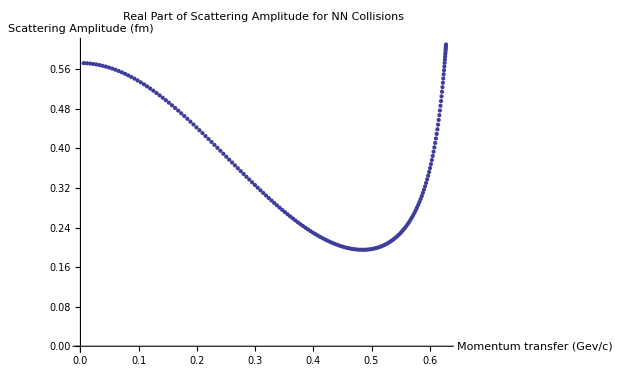

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Re[NN100[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

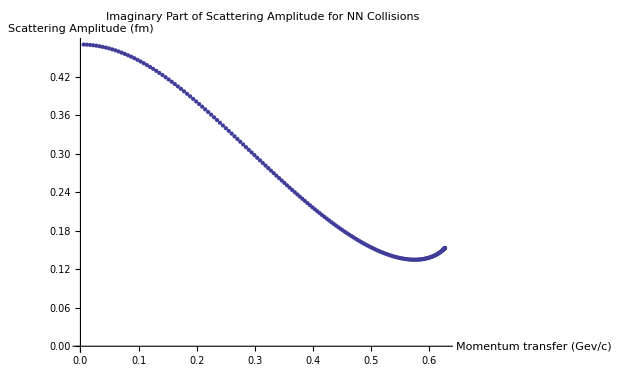

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Im[NN100[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

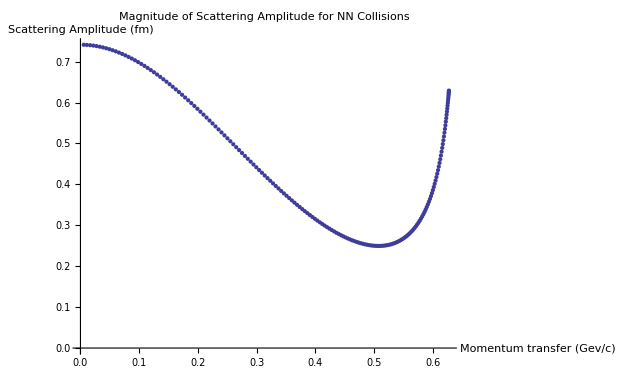

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

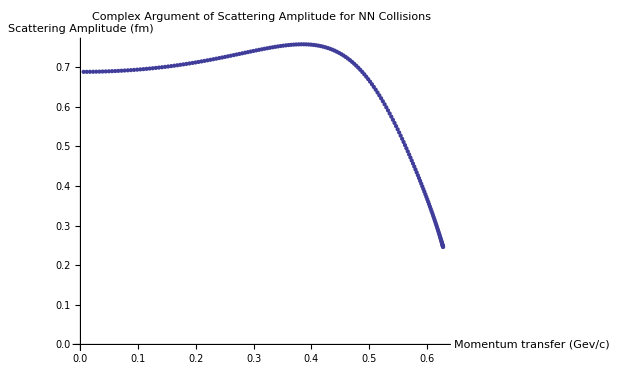

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{σ→5.84508,βre→5.90368}

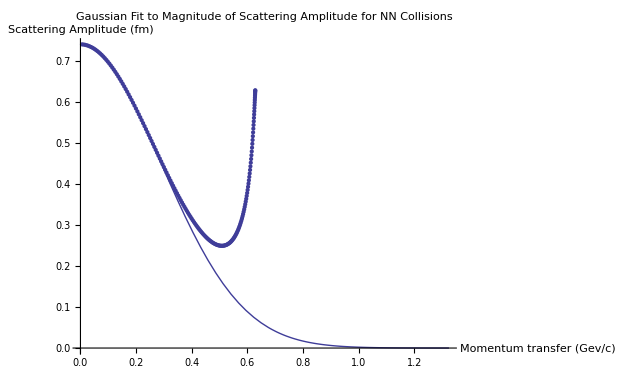

```mathematica
Npts=50;
FindFit[Transpose[{NN100[[1;;Npts,1]],Abs[NN100[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 P}],ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→1.21713,βim→-0.603069}

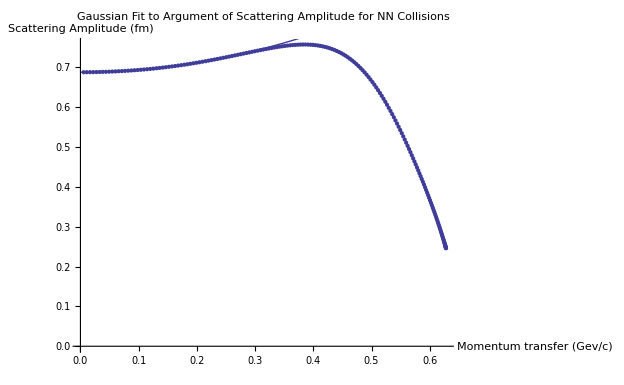

```mathematica
FindFit[Transpose[{NN100[[1;;Npts,1]],Arg[NN100[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 P}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.5626620954511277&&ρ==1.217127351734708,{σ,ρ}]
```

Fitted parameters:

```mathematica
σ=5.845078072031535;
ρ=1.217127351734708;
β=5.9036808770040965-0.6030692586212671 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

1.12575-1.11638 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber aNNroximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

231.644

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

1.12575-1.11638 ⅈ

```mathematica
U[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U[0]
```

-126.838-33.3033 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

```mathematica
Quiet[Table[{q,Abs[U[Sqrt[q]]]},{q,0.001,1.001,.1}]]
```

{{0.001,130.382},{0.101,73.3329},{0.201,41.7268},{0.301,24.4224},{0.401,15.0921},{0.501,10.0862},{0.601,7.30257},{0.701,5.60532},{0.801,4.44796},{0.901,3.59107},{1.001,2.92934}}

```mathematica
interp1=Interpolation[{{0.001,130.3816922241354},{0.101,73.33288376119694},{0.201,41.72678292258866},{0.30100000000000005,24.422391806011827},{0.401,15.092091368526807},{0.501,10.086166123662311},{0.6010000000000001,7.30257070783558},{0.7010000000000001,5.60531682565113},{0.801,4.447964079351995},{0.901,3.591068886299744},{1.001,2.9293436114889104}}];
```

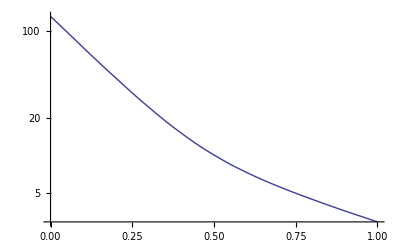

```mathematica
Quiet[LogPlot[interp1[t],{t,0,1}]]
```

The magnitude seems to be well approximated by a gaussian.

```mathematica
Quiet[Table[{q,Arg[U[Sqrt[q]]]},{q,0,1,.01}]]
```

{{0.001,-2.88553},{0.101,-2.9773},{0.201,-3.11838},{0.301,2.96508},{0.401,2.70837},{0.501,2.41741},{0.601,2.12833},{0.701,1.86611},{0.801,1.63505},{0.901,1.42816},{1.001,1.23695}}

```mathematica
interp2=Interpolation[{{0.001,-2.885530434856149},{0.101,-2.9772964586944504},{0.201,-3.118383266883238},{0.30100000000000005,2.96507550694934},{0.401,2.7083721617642196},{0.501,2.4174142092517},{0.6010000000000001,2.1283269557400892},{0.7010000000000001,1.8661131014697228},{0.801,1.6350467922104788},{0.901,1.4281555855421826},{1.001,1.2369548207819576}}];
```

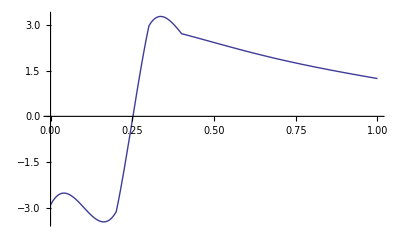

```mathematica
Quiet[Plot[interp2[t],{t,0,1}]]
```

```mathematica
Quiet[U[.1]]
```

-119.94-30.5652 ⅈ

```mathematica
γ=100*Quiet[(Log[U[0]]-Log[U[0.1]])]
```

5.77951+0.724292 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

1.00772-0.46339 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+β))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1[0]+FD1[0]]/Im[F0[0]+FO1[0]+FD1[0]]
```

-0.00141183

The first order correction is about 0.1% at 100 MeV.

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]+F0[0]]
```

231.644

-0.326581

231.318

```mathematica
FO1[0]
```

0.0209147+0.189762 ⅈ

```mathematica
FD1[0]
```

-0.185386-0.196501 ⅈ